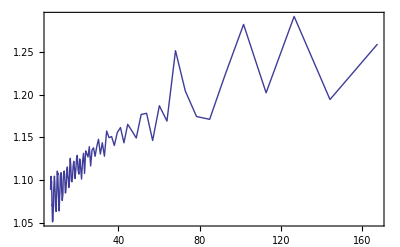

```mathematica
filedir="/home/daneel/workspace/2d_ff_notlhalf_latest/2d_ff_nothalf_fourth/transmag/";

SetDirectory[filedir];
filenames=FileNames[];
μ=1.0;
cycles=50.0;
filenos=Length[filenames];
avgQ=Table[data=Import[filenames[[i]],"Table"];fname=filenames[[i]];{2*μ/(StringSplit[fname,"_"][[3]]//ToExpression),(Select[data,#[[1]]<cycles &][[All,2]]//Mean) / data[[1,2]]},{i,1,filenos}];
sdQ=Table[data=Import[filenames[[i]],"Table"];fname=filenames[[i]];{2*μ/(StringSplit[fname,"_"][[3]]//ToExpression),(Select[data,#[[1]]<cycles &][[All,2]]//StandardDeviation) / data[[1,2]]},{i,1,filenos}];
ListPlot[avgQ,Joined->True,Frame->True,Axes->False]
outfileavg=StringJoin["2dlattice_avgQ_periods_",ToString[cycles],"txt"];
```

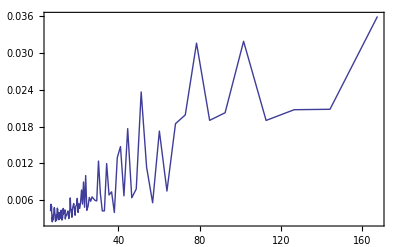

```mathematica
sdQ=Table[data=Import[filenames[[i]],"Table"];fname=filenames[[i]];{2*μ/(StringSplit[fname,"_"][[3]]//ToExpression),(Select[data,#[[1]]<cycles &][[All,2]]//StandardDeviation) / data[[1,2]]},{i,1,filenos}];
ListPlot[sdQ,Joined->True,Frame->True,Axes->False]
outfilesd=StringJoin["2dlattice_sdQ_periods_",ToString[cycles],"txt"];
```

```mathematica
Export[outfileavg,avgQ,"Table"];
Export[outfilesd,sdQ,"Table"];
```